```mathematica
SetDirectory[NotebookDirectory[]];
covData=Import["data/cov_mat.txt","Table"];
opts=covData[[;;,1]];
covs=Table[Transpose[{opts,covData[[;;,i]]}],{i,2,Length[covData[[1]]]}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
covTarget=Import["data/cov_mat_targets.txt","Table"][[1]];
```

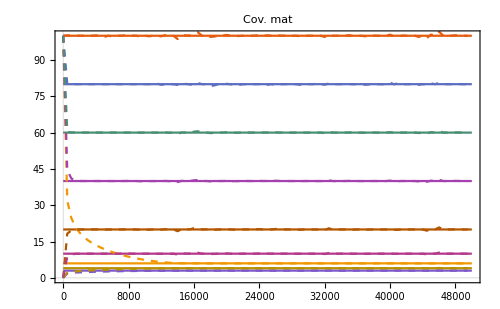

```mathematica
pCov=Show[
ListLinePlot[Table[{{0,x},{50000,x}},{x,covTarget}]],
ListLinePlot[covs,PlotStyle->Dashed],
ImageSize->500,
PlotLabel->"Cov. mat",
FrameLabel->{"Optimization step"}
]
```

```mathematica
CreateDirectory["figures"];
Export["figures/cov.png",pCov,ImageResolution->200]
```

CreateDirectory::filex: /Users/oernst/software_private/ggm_inversion/test/output/test_5d_adam/figures already exists.

figures/cov.png

```mathematica
SetDirectory[NotebookDirectory[]];
precData=Import["data/prec_mat.txt","Table"];
opts=precData[[;;,1]];
precs=Table[Transpose[{opts,precData[[;;,i]]}],{i,2,Length[covData[[1]]]}];
```

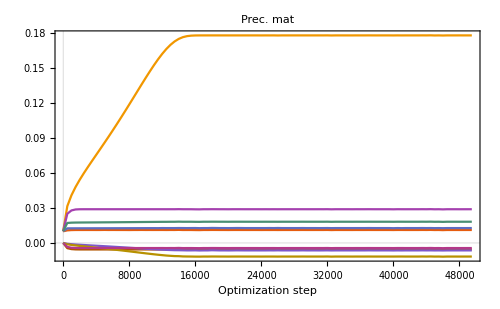

```mathematica
pPrec=ListLinePlot[precs,PlotRange->All,PlotLabel->"Prec. mat",FrameLabel->{"Optimization step"},ImageSize->500]
```

```mathematica
CreateDirectory["figures"];
Export["figures/prec.png",pPrec,ImageResolution->200]
```

CreateDirectory::filex: /Users/oernst/software_private/ggm_inversion/test/output/test_5d_adam/figures already exists.

figures/prec.png